# calcolo zeri-poli - incubatrice

```mathematica
j:=7
kp:=10*j
ki:=0.10*j
kd:=100*j
(*a:=-0.0022126*)
a:=-0.0022
b:=0.00034102
```

```mathematica
Gs[s_]:=b/(s-a)
Cs[s_]:=kp+ki/s+s*kd
Ws[s_]:=(Gs[s]*Cs[s])/(1+Gs[s]*Cs[s])
WsSimp[s_]:=Together[Ws[s]]
```

```mathematica
sys=TransferFunctionModel[Ws[s],s]
poli=TransferFunctionPoles[sys]
zeri=TransferFunctionZeros[sys]
```

{{{-0.0105236-0.00905348 ⅈ,-0.0105236+0.00905348 ⅈ,-0.0022,0}}}

{{{-0.0887298,-0.0112702,-0.0022,0}}}

```mathematica
Solve[Numerator[WsSimp[s]]==0,s]
Solve[Denominator[WsSimp[s]]==0,s]
```

{{s→-0.0887298},{s→-0.0112702}}

{{s→-0.0105236-0.00905348 ⅈ},{s→-0.0105236+0.00905348 ⅈ}}

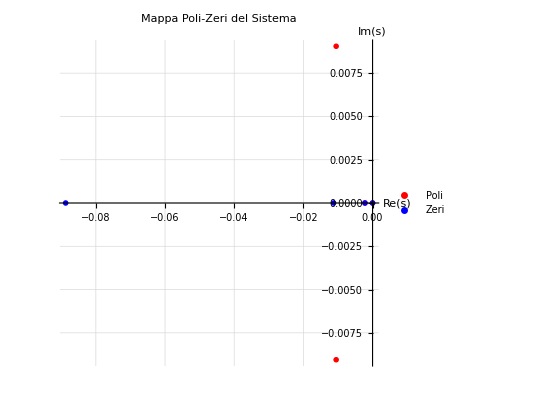

```mathematica
poliList:=Flatten[poli]
zeriList:=Flatten[zeri]
ComplexListPlot[{poliList,zeriList},
PlotMarkers->{{"X",16},{"O",16}},
PlotStyle->{Red,Blue},
PlotLegends->{"Poli","Zeri"},
AxesLabel->{"Re(s)","Im(s)"},
PlotLabel->"Mappa Poli-Zeri del Sistema",
GridLines->Automatic,
PlotRange->All,
AspectRatio->1
]
```

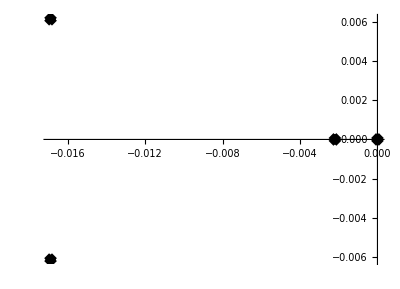

```mathematica
RootLocusPlot[sys,{k,0,1}]
```

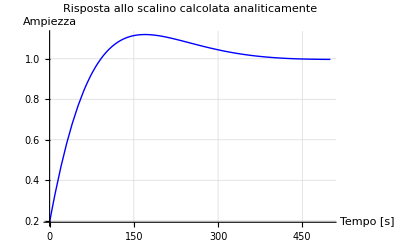

```mathematica
rispScalino=OutputResponse[sys,UnitStep[t],t];
Plot[Evaluate[rispScalino],
{t,0,500},
PlotRange->All,
GridLines->Automatic,
AxesLabel->{"Tempo [s]","Ampiezza"},
PlotLabel->"Risposta allo scalino calcolata analiticamente",
PlotStyle->{Thick,Blue}
]
```

----------

G(s) = b/(s-a)
C(s) = (k_d * s^2 + k_p * s + k_i)/s
L(s) = (b*k_d * s^2 + b*k_p * s + b*k_i)/(s * (s - a)) = (D * s^2 + P * s + I)/(s * (s - a))
W_r(s) = L(s) / (1 + L(s)) = ((D * s^2 + P * s + I) / ((D + 1) * s^2 + (P - a) * s + I)
z0 = (-P + Sqrt[P^2 - 4*D*I]) /  2D
z1 = (-P - Sqrt[P^2 - 4*D*I]) /  2D
p0  = (-(P-a) + Sqrt[(P-a)^2 - 4*(D+1)*I]) /  2(D+1)
p1  = (-(P-a) + Sqrt[(P-a)^2 - 4*(D+1)*I]) /  2(D+1)

```mathematica
(*z0:=(-b*kp+Sqrt[b*kp^2 - 4*b*kd*b*ki])/(2*b*kd)
z1:=(-b*kp-Sqrt[b*kp^2 - 4*b*kd*b*ki])/(2*b*kd)
p0:=(-(b*kp-a)+Sqrt[(b*kp-a)^2 - 4*(b*kd+1)*b*ki])/(2*(b*kd+1))
p1:=(-(b*kp-a)-Sqrt[(b*kp-a)^2 - 4*(b*kd+1)*b*ki])/(2*(b*kd+1))*(
```

```mathematica
(*{z0,z1,p0, p1}*(
```

```mathematica
(*Plot[{p0, p1},{x,0,1}]*)
```

```mathematica
(*wn:=Sqrt[b*ki]
e:=(b*kp-a)/(2*wn)
mp:=Exp[-Pi*e/Sqrt[1-e^2]]
ts:=3/(e*wn)
tr:=1.8/wn*(
```

```mathematica
(*{wn, e, mp, ts, tr}*(
```

```mathematica
(*Plot[e,{x,0,1}]*)
```